```mathematica
(*Project Euler*)
```

```mathematica
(*501: Eight Divisors*)
v=0;SetSharedVariable[v];ParallelDo[If[Length@Divisors@i==8,v+=1],{i,0,160}];v
```

22

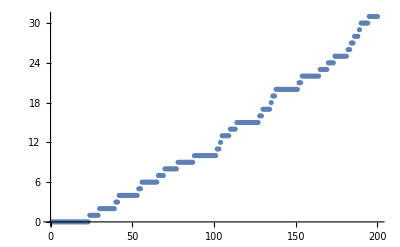

```mathematica
ListPlot[Length@Select[Range@#,Length@Divisors@#==8&]&/@Range@200]
```